```mathematica
dataC1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/C1.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
```

```mathematica
dataC1//TableForm
```

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXC1=MapAt[dropLastDot@*ToString,dataC1,{{2;;,All}}];
forTeXC1//TeXForm
```

```mathematica
dataC2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/C2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
forTeXC2=MapAt[dropLastDot@*ToString,dataC2,{{2;;,All}}];
forTeXC2//TeXForm
```

{{Сn , нФ,fon, кГц,U, B,E, B,L, мкГн,ƍ, Ом,Zрез, Ом,Q,RΣ, Ом,Rsmax, Ом,RL, Ом},{25.1,32.1,2.18,0.37,980.4,197.6,5939.,30.1,6.58,0.2,2.9},{33.2,27.8,1.62,0.37,988.2,172.5,4413.4,25.6,6.74,0.17,3.1},{47.3,23.2,1.23,0.37,996.,145.1,3350.9,23.1,6.28,0.15,2.6},{57.4,21.3,1.04,0.37,973.7,130.2,2833.3,21.8,5.99,0.13,2.4},{67.5,19.5,0.88,0.37,987.9,121.,2397.4,19.8,6.1,0.12,2.5},{82.7,17.7,0.74,0.37,978.7,108.8,2016.,18.5,5.87,0.11,2.3},{101.6,16.,0.62,0.37,974.9,98.,1689.1,17.2,5.68,0.1,2.1}}

\left(
\begin{array}{ccccccccccc}
 \text{$\unicode{0421}$n , $\unicode{043d}\unicode{0424}$} & \text{fon, $\unicode{043a}\unicode{0413}\unicode{0446}$} & \text{U, B} & \text{E, B} &
   \text{L, $\unicode{043c}\unicode{043a}\unicode{0413}\unicode{043d}$} & \text{$\unicode{018d}$, $\unicode{041e}\unicode{043c}$} &
   \text{Z$\unicode{0440}\unicode{0435}\unicode{0437}$, $\unicode{041e}\unicode{043c}$} & \text{Q} & \text{R$\Sigma $, $\unicode{041e}\unicode{043c}$}
   & \text{Rsmax, $\unicode{041e}\unicode{043c}$} & \text{RL, $\unicode{041e}\unicode{043c}$} \\
 25.1 & 32.1 & 2.18 & 0.37 & 980.4 & 197.6 & 5939 & 30.1 & 6.58 & 0.2 & 2.9 \\
 33.2 & 27.8 & 1.62 & 0.37 & 988.2 & 172.5 & 4413.4 & 25.6 & 6.74 & 0.17 & 3.1 \\
 47.3 & 23.2 & 1.23 & 0.37 & 996 & 145.1 & 3350.9 & 23.1 & 6.28 & 0.15 & 2.6 \\
 57.4 & 21.3 & 1.04 & 0.37 & 973.7 & 130.2 & 2833.3 & 21.8 & 5.99 & 0.13 & 2.4 \\
 67.5 & 19.5 & 0.88 & 0.37 & 987.9 & 121 & 2397.4 & 19.8 & 6.1 & 0.12 & 2.5 \\
 82.7 & 17.7 & 0.74 & 0.37 & 978.7 & 108.8 & 2016 & 18.5 & 5.87 & 0.11 & 2.3 \\
 101.6 & 16 & 0.62 & 0.37 & 974.9 & 98 & 1689.1 & 17.2 & 5.68 & 0.1 & 2.1 \\
\end{array}
\right)

```mathematica
dataF=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/F.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
dataF//TableForm
```

{{f, кГц,U, B,f/fo,U/Uo,,f, кГц,U, B,f/fo,U/Uo},{27.14,0.54,0.976,0.593,0.,18.6,0.22,0.954,0.458},{27.18,0.56,0.978,0.615,0.,18.68,0.24,0.958,0.5},{27.27,0.61,0.981,0.67,0.,18.75,0.26,0.962,0.542},{27.33,0.66,0.983,0.725,0.,18.83,0.28,0.966,0.583},{27.46,0.74,0.988,0.813,0.,18.92,0.31,0.97,0.646},{27.54,0.79,0.991,0.868,0.,19.06,0.36,0.977,0.75},{27.59,0.83,0.992,0.912,0.,19.11,0.37,0.98,0.771},{27.93,0.89,1.005,0.978,0.,19.3,0.45,0.99,0.938},{27.99,0.89,1.007,0.978,0.,19.68,0.44,1.009,0.917},{28.01,0.86,1.008,0.945,0.,19.77,0.41,1.014,0.854},{28.14,0.79,1.012,0.868,0.,19.8,0.4,1.015,0.833},{28.21,0.74,1.015,0.813,0.,19.94,0.35,1.023,0.729},{28.23,0.73,1.014,0.802,0.,20.,0.33,1.026,0.688},{28.27,0.7,1.017,0.769,0.,20.06,0.31,1.029,0.646},{28.34,0.66,1.019,0.725,0.,20.16,0.28,1.034,0.583},{28.5,0.56,1.025,0.615,0.,20.37,0.23,1.045,0.479}}

f, кГц | U, B | f/fo | U/Uo |  | f, кГц | U, B | f/fo | U/Uo
27.14 | 0.54 | 0.976 | 0.593 | 0. | 18.6 | 0.22 | 0.954 | 0.458
27.18 | 0.56 | 0.978 | 0.615 | 0. | 18.68 | 0.24 | 0.958 | 0.5
27.27 | 0.61 | 0.981 | 0.67 | 0. | 18.75 | 0.26 | 0.962 | 0.542
27.33 | 0.66 | 0.983 | 0.725 | 0. | 18.83 | 0.28 | 0.966 | 0.583
27.46 | 0.74 | 0.988 | 0.813 | 0. | 18.92 | 0.31 | 0.97 | 0.646
27.54 | 0.79 | 0.991 | 0.868 | 0. | 19.06 | 0.36 | 0.977 | 0.75
27.59 | 0.83 | 0.992 | 0.912 | 0. | 19.11 | 0.37 | 0.98 | 0.771
27.93 | 0.89 | 1.005 | 0.978 | 0. | 19.3 | 0.45 | 0.99 | 0.938
27.99 | 0.89 | 1.007 | 0.978 | 0. | 19.68 | 0.44 | 1.009 | 0.917
28.01 | 0.86 | 1.008 | 0.945 | 0. | 19.77 | 0.41 | 1.014 | 0.854
28.14 | 0.79 | 1.012 | 0.868 | 0. | 19.8 | 0.4 | 1.015 | 0.833
28.21 | 0.74 | 1.015 | 0.813 | 0. | 19.94 | 0.35 | 1.023 | 0.729
28.23 | 0.73 | 1.014 | 0.802 | 0. | 20. | 0.33 | 1.026 | 0.688
28.27 | 0.7 | 1.017 | 0.769 | 0. | 20.06 | 0.31 | 1.029 | 0.646
28.34 | 0.66 | 1.019 | 0.725 | 0. | 20.16 | 0.28 | 1.034 | 0.583
28.5 | 0.56 | 1.025 | 0.615 | 0. | 20.37 | 0.23 | 1.045 | 0.479

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
```

```mathematica
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicksX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,2}]
myTicksY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
interF1=Interpolation@dataF⟦2;;,{1,2}⟧;
{minF1,maxF1}=MinMax@dataF⟦2;;,1⟧;
{minF2,maxF2}=MinMax@dataF⟦2;;,6⟧;
interF2=Interpolation@dataF⟦2;;,{6,7}⟧;
```

```mathematica
Show[Plot[interF2@x,{x,minF2,maxF2},
GridLines->{grids@0.5,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f, кГц","U, В"},
AxesStyle->Directive[Large,Black],
PlotStyle->Thickness@0.003,
PlotRange->{{17.6,29},{0,0.99}},
ImageSize->1000],ListPlot[dataF⟦2;;,{6,7}⟧,PlotMarkers->{Automatic, 12}], Plot[interF1@x,{x,minF1,maxF1},
PlotStyle->Thickness@0.003,
ImageSize->1000],ListPlot[dataF⟦2;;,{1,2}⟧,PlotMarkers->{Automatic, 12}]]
```

Фитирование гауссом

```mathematica
f[a_,x0_,b_][x_]:=a*Exp[-((x-x0)/b)^2];
fitting@data_:=
Module[{
start=data⟦MaximalBy[FindPeaks@data⟦All,2⟧,#⟦2⟧&]⟦1,1⟧⟧,
nlm,a=1,x0,b,x},

nlm=
NonlinearModelFit[
data,
f[a,x0,b][x],
{
(*{a,start⟦2⟧},*)
{x0,start⟦1⟧},
{b,√(#2^2/(4#3^2)-#1/#3//RealAbs)&@@CoefficientList[Fit[data,{1,x,x^2},x],x]}
},x,
Weights->data⟦All,2⟧^4];

Print[nlm@"ParameterTable"/.Thread[{a,x0,b}->{"a","x0","b"}]];
nlm@"Function"
](*end of fitting definition*)
```

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 1.00052 | 0.000426913 | 2343.61 | 3.79375×10^-43
b | 0.0290721 | 0.000876288 | 33.1764 | 1.87674×10^-15

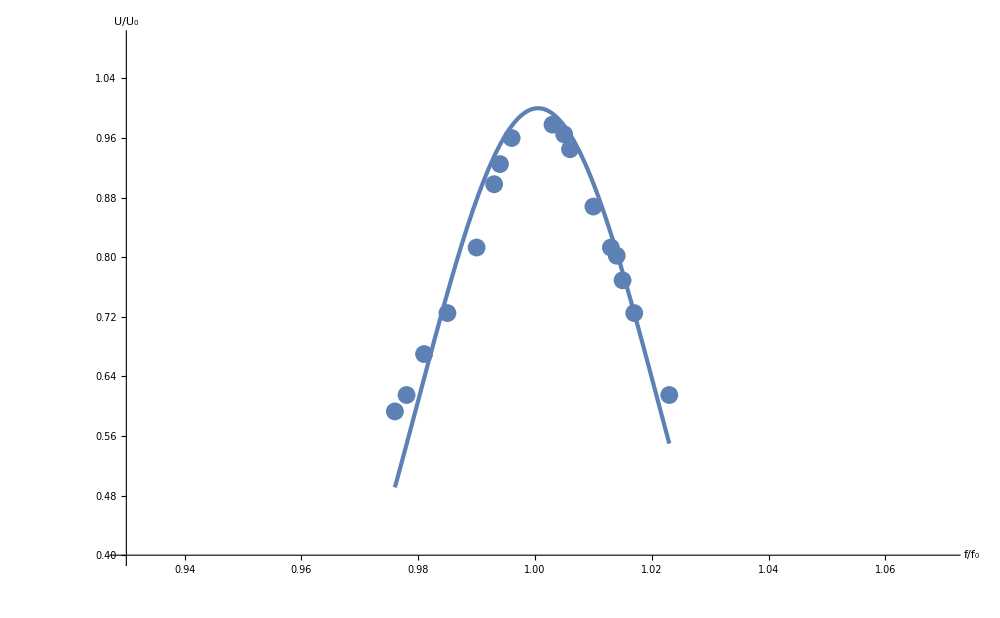

```mathematica
dataForFit=dataFf⟦2;;,{3,4}⟧;
fitDataFf=fitting@dataForFit;
With[{minMaxX=MinMax@dataForFit⟦All,1⟧},
Show[Plot[fitDataFf@x,{x,minMaxX⟦1⟧,minMaxX⟦2⟧},

GridLines->{grids@0.005,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f/f_0","U/U_0"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003},
PlotRange->{{0.93,1.07},{0.4,1.09}},
ImageSize->1000],ListPlot@dataForFit
]
]
```

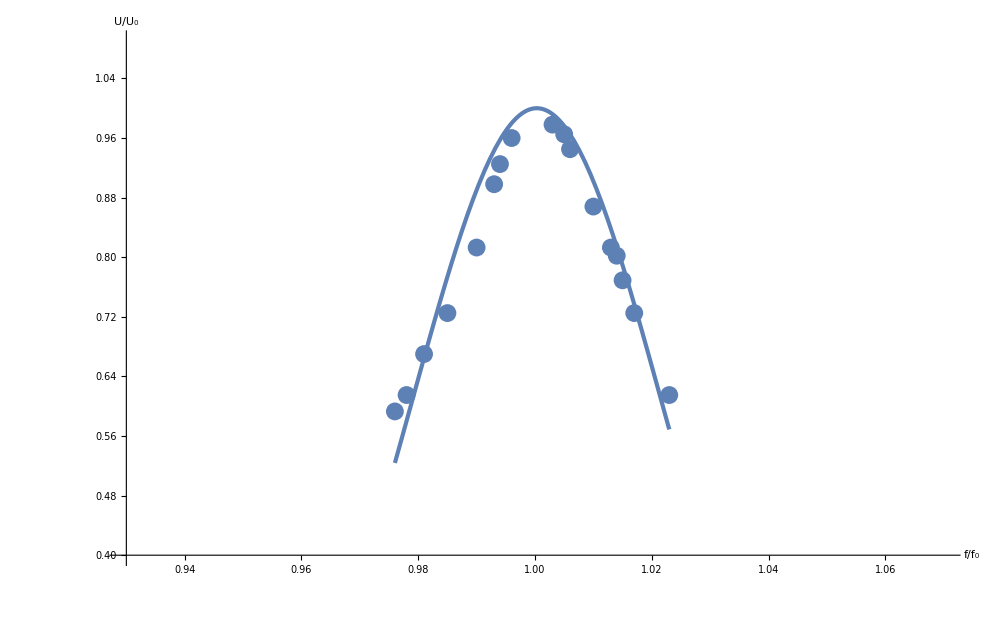

```mathematica
dataFf=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/Ff.xlsx"]⟦1,All,1;;⟧,Except@{"Таблица 1"|"",""..}];
dataFf//TableForm
```

f, кГц | U, B | f/fo | U/Uo |  | f, кГц | U, B | f/fo | U/Uo
27.14 | 0.54 | 0.976 | 0.593 | 0. | 18.6 | 0.22 | 0.954 | 0.458
27.18 | 0.56 | 0.978 | 0.615 | 0. | 18.68 | 0.24 | 0.958 | 0.5
27.27 | 0.61 | 0.981 | 0.67 | 0. | 18.75 | 0.26 | 0.962 | 0.542
27.33 | 0.66 | 0.985 | 0.725 | 0. | 18.83 | 0.28 | 0.966 | 0.583
27.46 | 0.74 | 0.99 | 0.813 | 0. | 18.92 | 0.31 | 0.97 | 0.646
27.54 | 0.79 | 0.993 | 0.898 | 0. | 19.06 | 0.36 | 0.977 | 0.75
27.59 | 0.83 | 0.994 | 0.925 | 0. | 19.11 | 0.37 | 0.989 | 0.9
1. | 0.91 | 0.996 | 0.96 | 0. | 1. | 0.91 | 1.001 | 0.99
27.93 | 0.89 | 1.003 | 0.978 |  | 19.3 | 0.45 | 1.005 | 0.938
27.99 | 0.89 | 1.005 | 0.965 |  | 19.68 | 0.44 | 1.009 | 0.917
28.01 | 0.86 | 1.006 | 0.945 |  | 19.77 | 0.41 | 1.014 | 0.854
28.14 | 0.79 | 1.01 | 0.868 |  | 19.8 | 0.4 | 1.015 | 0.833
28.21 | 0.74 | 1.013 | 0.813 |  | 19.94 | 0.35 | 1.023 | 0.729
28.23 | 0.73 | 1.014 | 0.802 |  | 20. | 0.33 | 1.026 | 0.688
28.27 | 0.7 | 1.015 | 0.769 |  | 20.06 | 0.31 | 1.029 | 0.646
28.34 | 0.66 | 1.017 | 0.725 |  | 20.16 | 0.28 | 1.034 | 0.583
28.5 | 0.56 | 1.023 | 0.615 |  | 20.37 | 0.23 | 1.045 | 0.479

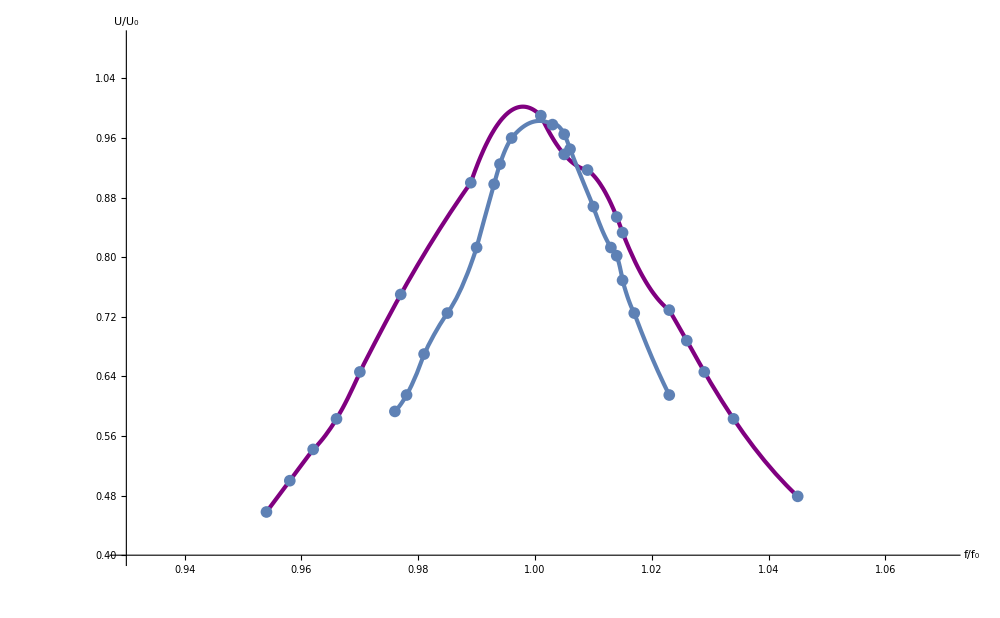

```mathematica
interFF1=Interpolation[dataFf⟦2;;,{3,4}⟧,InterpolationOrder->2];
{minFF1,maxFF1}=MinMax@dataFf⟦2;;,3⟧;
{minFF2,maxFF2}=MinMax@dataFf⟦2;;,8⟧;
interFF2=Interpolation[dataFf⟦2;;,{8,9}⟧, InterpolationOrder->2];
Show[Plot[interFF2@x,{x,minFF2,maxFF2},
GridLines->{grids@0.005,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f/f_0","U/U_0"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
PlotRange->{{0.93,1.07},{0.4,1.09}},
ImageSize->1000],ListPlot[dataFf⟦2;;,{8,9}⟧,PlotMarkers->{Automatic, 12}], Plot[interFF1@x,{x,minFF1,maxFF1},
PlotStyle->Thickness@0.003,
ImageSize->1000],ListPlot[dataFf⟦2;;,{3,4}⟧,PlotMarkers->{Automatic, 12}]]
```

```mathematica
dataFf=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/Ff.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

{{f, кГц,U, B,f/fo,U/Uo,,f, кГц,U, B,f/fo,U/Uo},{27.14,0.54,0.976,0.593,0.,18.6,0.22,0.954,0.458},{27.18,0.56,0.978,0.615,0.,18.68,0.24,0.958,0.5},{27.27,0.61,0.981,0.67,0.,18.75,0.26,0.962,0.542},{27.33,0.66,0.983,0.725,0.,18.83,0.28,0.966,0.583},{27.46,0.74,0.988,0.813,0.,18.92,0.31,0.97,0.646},{27.54,0.79,0.994,0.868,0.,19.06,0.36,0.977,0.75},{27.59,0.83,0.998,0.912,0.,19.11,0.37,0.989,0.9},{1.,0.91,1.002,0.99,0.,1.,0.91,1.001,0.99},{27.93,0.89,1.005,0.978,0.,19.3,0.45,1.005,0.938},{27.99,0.89,1.007,0.978,0.,19.68,0.44,1.009,0.917},{28.01,0.86,1.008,0.945,0.,19.77,0.41,1.014,0.854},{28.14,0.79,1.012,0.868,0.,19.8,0.4,1.015,0.833},{28.21,0.74,1.015,0.813,0.,19.94,0.35,1.023,0.729},{28.23,0.73,1.016,0.802,0.,20.,0.33,1.026,0.688},{28.27,0.7,1.017,0.769,0.,20.06,0.31,1.029,0.646},{28.34,0.66,1.019,0.725,0.,20.16,0.28,1.034,0.583},{28.5,0.56,1.025,0.615,0.,20.37,0.23,1.045,0.479}}

```mathematica
dataFi1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/Fi.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
dataFi1//TableForm
```

U, B | f/fo |  |  | X/Xo
0.29 | 0.949 | 2.2 | 4. | 0.55
0.76 | 0.989 | 3. | 3.9 | 0.77
0.9 | 1.003 | 3.9 | 3.8 | 1.03
0.64 | 0.983 | 2.8 | 3.9 | 0.72
0.26 | 0.944 | 2.4 | 4. | 0.6
0.38 | 0.963 | 2.5 | 4. | 0.63
0.77 | 0.99 | 3.1 | 3.8 | 0.82
0.5 | 0.974 | 2.7 | 3.9 | 0.69
0.82 | 1.007 | 4.1 | 3.7 | 1.11
0.28 | 1.052 | 4.9 | 3.6 | 1.36
0.56 | 1.022 | 4.7 | 3.7 | 1.27
0.83 | 1.008 | 4.2 | 3.7 | 1.14
0.46 | 1.03 | 4.8 | 3.7 | 1.3
0.6 | 1.02 | 4.6 | 3.7 | 1.24
0.74 | 1.012 | 4.4 | 3.7 | 1.19

```mathematica
dataFi2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/Fi1.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
dataFi2//TableForm
```

U, B | f/fo |  |  | X/Xo
0.29 | 0.967 | 4. | 5.8 | 0.69
0.42 | 0.986 | 4.6 | 5.7 | 0.81
0.35 | 0.976 | 4.2 | 5.7 | 0.74
0.23 | 0.953 | 3.8 | 5.7 | 0.67
0.18 | 0.937 | 3.6 | 5.8 | 0.62
0.47 | 0.994 | 5. | 5.5 | 0.91
0.48 | 1. | 5.3 | 5.4 | 0.98
0.38 | 0.981 | 4.4 | 5.5 | 0.8
0.44 | 1.01 | 5.9 | 5.4 | 1.09
0.26 | 1.039 | 6.7 | 5.2 | 1.29
0.15 | 1.074 | 7. | 5. | 1.4
0.24 | 1.043 | 6.8 | 5.2 | 1.31
0.42 | 1.014 | 6.1 | 5.3 | 1.15
0.46 | 1.007 | 5.8 | 5.4 | 1.07
0.37 | 1.02 | 6.4 | 5.3 | 1.21
0.31 | 1.029 | 6.6 | 5.2 | 1.27

```mathematica
inter1=Interpolation[dataFi1⟦2;;,{2,5}⟧,InterpolationOrder->1];
{min1,max1}=MinMax@dataFi1⟦2;;,2⟧;
{min2,max2}=MinMax@dataFi2⟦2;;,2⟧;
inter2=Interpolation[dataFi2⟦2;;,{2,5}⟧,InterpolationOrder->1];
```

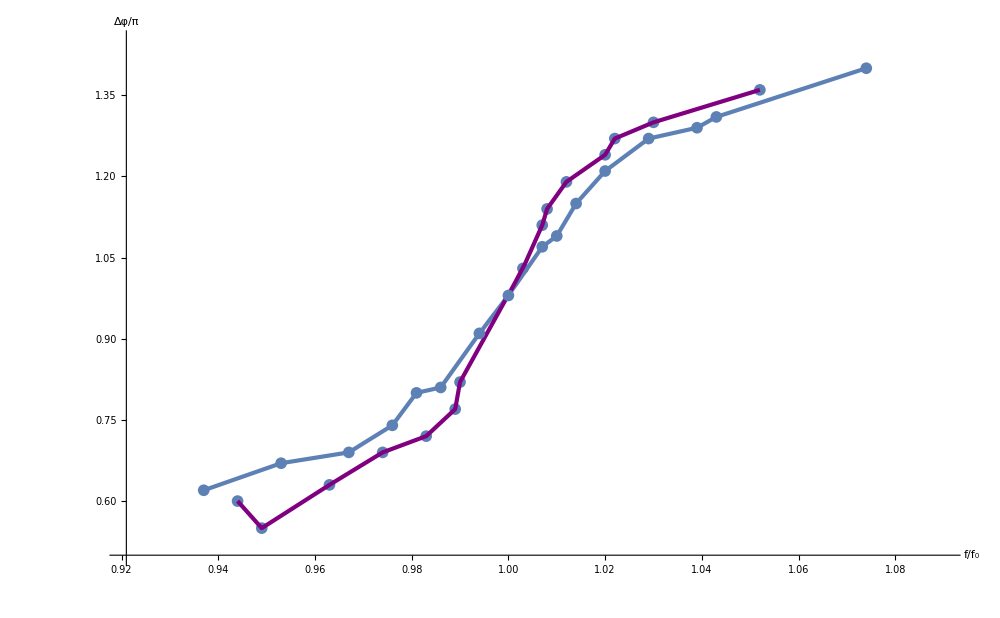

```mathematica
Show[Plot[inter2@x,{x,min2,max2},
GridLines->{grids@0.01,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f/f_0","Δφ/π"},
AxesStyle->Directive[Large,Black],
PlotStyle->Thickness@0.003,
PlotRange->{{0.921,1.09},{0.5,1.45}},
ImageSize->1000],ListPlot[dataFi1⟦2;;,{2,5}⟧,PlotMarkers->{Automatic, 12}], Plot[inter1@x,{x,min1,max1},
PlotStyle->{Thickness@0.003, Purple},
ImageSize->1000],ListPlot[dataFi2⟦2;;,{2,5}⟧,PlotMarkers->{Automatic, 12}]]
```

```mathematica
interFi1=Interpolation[dataFi⟦2;;,{3,4}⟧,InterpolationOrder->2];
{minFi1,maxFi1}=MinMax@dataFi⟦2;;,3⟧;
{minFi2,maxFi2}=MinMax@dataFi⟦2;;,8⟧;
interFi2=Interpolation[dataFi⟦2;;,{8,9}⟧, InterpolationOrder->2];
Show[Plot[interFF2@x,{x,minFF2,maxFF2},
GridLines->{grids@0.5,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f/f_0","U/U_0"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
PlotRange->{{0.93,1.07},{0.4,1.09}},
ImageSize->1000],ListPlot[dataF⟦2;;,{8,9}⟧,PlotMarkers->{Automatic, 12}], Plot[interFF1@x,{x,minFF1,maxFF1},
PlotStyle->Thickness@0.003,
ImageSize->1000],ListPlot[dataF⟦2;;,{3,4}⟧,PlotMarkers->{Automatic, 12}]]
```

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/123/R.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataR//TableForm
```

fon, кГц | RL, Ом |  | 
32.1 | 2.9 | 0.1 | 0.15
27.8 | 2.8 | 0.1 | 0.14
23.2 | 2.6 | 0.1 | 0.12
21.3 | 2.3 | 0.1 | 0.11
19.5 | 2.4 | 0.1 | 0.09
17.7 | 2.3 | 0.1 | 0.08
16. | 2. | 0.1 | 0.07

```mathematica
orFit=(*Select[*)dataR⟦2;;,{2,1}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{32.1,2.9},{27.8,2.8},{23.2,2.6},{21.3,2.3},{19.5,2.4},{17.7,2.3},{16.,2.}}

| Estimate | Standard Error | t-Statistic | P-Value
x | 0.0521857 | 0.00776515 | 6.72051 | 0.00110514
1 | 1.2965 | 0.179602 | 7.21878 | 0.000795419

1.2965+0.0521857 #1&

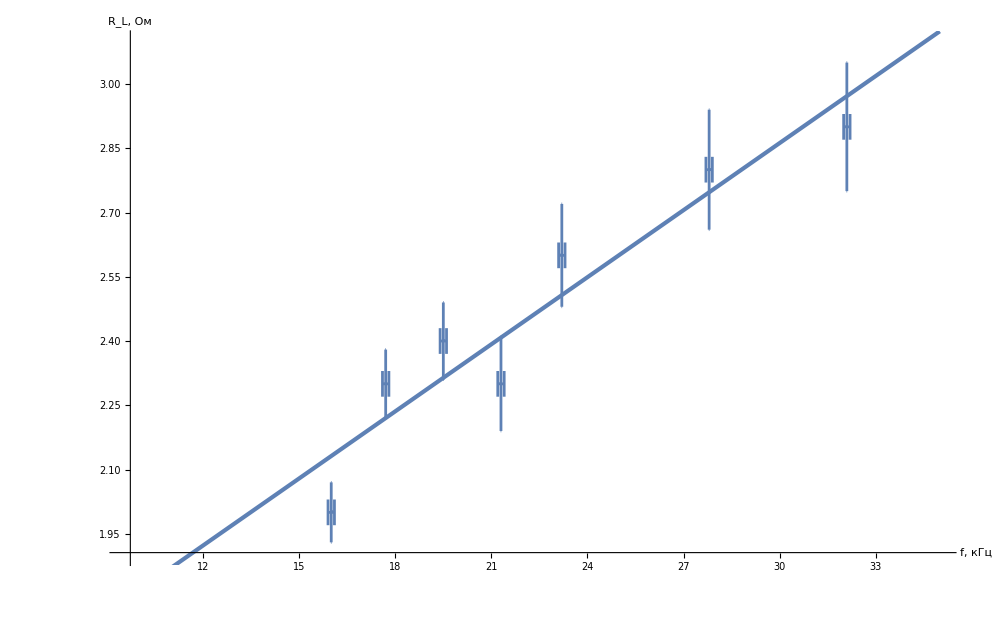

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,2,3,4}⟧,
GridLines->{grids@0.5,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"f, кГц","R_L, Ом"},
ErrorBarFunction->Function[{coords,errors},{Thickness@0.002,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 },
PlotMarkers->{Automatic,0.01},
PlotRange->{{9.6,35},{1.9,3.1}},
ImageSize->1000],Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

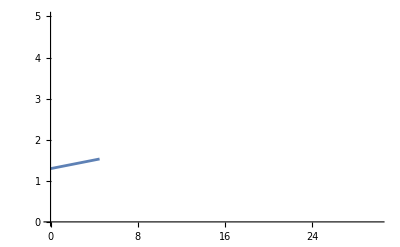

```mathematica
Plot[fit["Function"]@x,{x,0,4.5}, PlotStyle->Thickness@0.005, PlotRange->{{0,30},{0,5}}]
```

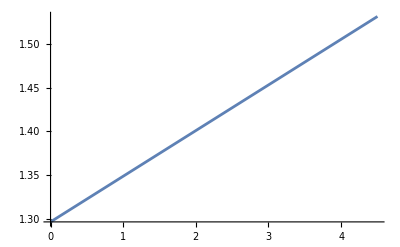

-Graphics-

```mathematica
print@x_:=(Print@x;x)
```